```mathematica
(*Problem 1*)
```

```mathematica
D[a*Exp[I*Ω*t],{t,2}]==-w0^2*a*Exp[I*Ω*t]+(2/3)*D[a*Exp[I*Ω*t],{t,3}]*(r0/l0)/w0//FullSimplify
```

(a ⅇ^(ⅈ t Ω) (2 ⅈ r0 Ω^3+3 l0 w0 (w0-Ω) (w0+Ω)))/(l0 w0)==0

```mathematica
(2 ⅈ r0 Ω^3+3 l0 w0 (w0-Ω) (w0+Ω))/( 3*l0 w0 )//FullSimplify
```

w0^2-Ω^2+(2 ⅈ r0 Ω^3)/(3 l0 w0)

```mathematica
D[ a*Exp[I*Ω*t],{t,2}]
```

-a ⅇ^(ⅈ t Ω) Ω^2

```mathematica
Solve[w0^2-Ω^2+(2 ⅈ r0 Ω^3)/(3 l0 w0)==0,Ω]//FullSimplify
```

```mathematica
Solve[-2*w0*(Ω+w0)==-(2*I/3)*(r0/l0)*(1/w0)*w0^3,Ω]//FullSimplify
```

{{Ω→(-1+(ⅈ r0)/(3 l0)) w0}}

```mathematica
Solve[(ⅈ r0 w0)/(3 l0)==I*g0/2,g0]
```

{{g0→(2 r0 w0)/(3 l0)}}

```mathematica
(*Problem 2*)
```

```mathematica
D[z0*Exp[I*w*t],{t,2}]
```

-ⅇ^(ⅈ t w) w^2 z0

```mathematica
D[z0*Exp[I*w*t],{t,3}]
```

-ⅈ ⅇ^(ⅈ t w) w^3 z0

```mathematica
Solve[2*w0*(w-w0)==(2*I/3)*(r0/l0)*w0^2 - q*EE/m,w]//FullSimplify
```

{{w→-(EE q)/(2 m w0)+w0+(ⅈ r0 w0)/(3 l0)}}

```mathematica
Solve[-2*w0*(w+w0)==-(2*I/3)*(r0/l0)*w0^2 - q*EE/m,w]//FullSimplify
```

{{w→(EE q)/(2 m w0)+(-1+(ⅈ r0)/(3 l0)) w0}}

```mathematica
Solve[w^2==w0^2+(2*I/3)*(r0/l0)*w^3/w0 - q*EE/(m*z0),z0]//FullSimplify
```

{{z0→(3 EE l0 q w0)/(2 ⅈ m r0 w^3-3 l0 m w^2 w0+3 l0 m w0^3)}}

```mathematica
D[Cos[t],t]
```

-Sin[t]

```mathematica
D[a*Exp[I*(w*t+p)],{t,2}]
```

-a ⅇ^(ⅈ (p+t w)) w^2

```mathematica
D[a*Exp[I*(w*t+p)],{t,1}]
```

ⅈ a ⅇ^(ⅈ (p+t w)) w

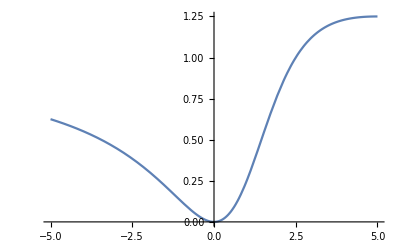

```mathematica
Plot[x^2/((x-1)^2+4),{x,-5,5}]
```